```mathematica
thing=1/4 (2 Delta sz+H1 sx Cos[phi]+H1 sy Sin[phi])+1/(32 ww)(H1^2 sz-2 H1^2 sz Cos[2 (phi+α0)]+4 (Delta H1 sx+H1D sy) Cos[phi+2 α0]+4 (H1D sx-Delta H1 sy) Sin[phi+2 α0])+1/(256 ww^2)(-8 Delta H1^2 sz-2 H1^3 sx Cos[phi]+8 Delta H1^2 sz Cos[2 (phi+α0)]-16 Delta^2 H1 sx Cos[phi+2 α0]+16 H1DD sx Cos[phi+2 α0]-32 Delta H1D sy Cos[phi+2 α0]+2 H1^3 sx Cos[3 phi+2 α0]-H1^3 sx Cos[3 phi+4 α0]-2 H1^3 sy Sin[phi]+24 H1 H1D sz Sin[2 (phi+α0)]-32 Delta H1D sx Sin[phi+2 α0]+16 Delta^2 H1 sy Sin[phi+2 α0]-16 H1DD sy Sin[phi+2 α0]+2 H1^3 sy Sin[3 phi+2 α0]+H1^3 sy Sin[3 phi+4 α0]);
```

```mathematica
sthing=thing/.{Delta->0,α0->0,H1D->0,H1DD->0,H1DDD->0}//FullSimplify//Collect[#,1/ww]&
```

(H1 (8 H1 sz-16 H1 sz Cos[2 phi]))/(256 ww)+1/256 H1 (64 sx Cos[phi]+64 sy Sin[phi])+(H1 (-2 H1^2 sx Cos[phi]+H1^2 sx Cos[3 phi]-2 H1^2 sy Sin[phi]+3 H1^2 sy Sin[3 phi]))/(256 ww^2)

```mathematica
ψ0={1,0};
ψ0=ψ0/Norm[ψ0];
gateAngle = Pi;
tMax = 2*gateAngle/H1;
```

```mathematica
ψf=MatrixExp[-I*tMax*sthing/.pms].ψ0//FullSimplify
```

{(√(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi])) Cos[(π √(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi])))/(128 ww^2)]+8 ⅈ H1 ww (-1+2 Cos[2 phi]) Sin[(π √(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi])))/(128 ww^2)])/(√(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi]))),-((ⅇ^(-(ⅈ π √(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi])))/(128 ww^2)) (-1+ⅇ^((ⅈ π √(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi])))/(64 ww^2))) (-ⅇ^(-3 ⅈ phi) H1^2+2 ⅇ^(3 ⅈ phi) H1^2-2 ⅇ^(ⅈ phi) (H1^2-32 ww^2)))/(2 √(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi]))))}

```mathematica
angles=BlochAngleCoordinatesFromState[ψf]//FullSimplify
```

{-π+Mod[π+Arg[-((ⅇ^(-(ⅈ π √(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi])))/(128 ww^2)) (-1+ⅇ^((ⅈ π √(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi])))/(64 ww^2))) (-ⅇ^(-3 ⅈ phi) H1^2+2 ⅇ^(3 ⅈ phi) H1^2-2 ⅇ^(ⅈ phi) (H1^2-32 ww^2)))/(√(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi]))))]-Arg[(√(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi])) Cos[(π √(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi])))/(128 ww^2)]+8 ⅈ H1 ww (-1+2 Cos[2 phi]) Sin[(π √(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi])))/(128 ww^2)])/(√(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi])))],2 π],2 ArcCos[Abs[(√(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi])) Cos[(π √(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi])))/(128 ww^2)]+8 ⅈ H1 ww (-1+2 Cos[2 phi]) Sin[(π √(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi])))/(128 ww^2)])/(√(9 H1^4-64 H1^2 ww^2+4096 ww^4-4 H1^4 (2 Cos[2 phi]-Cos[4 phi]+Cos[6 phi])))]]}

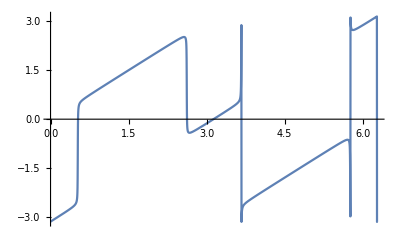

```mathematica
Plot[angles[[1]]/.{ww->1,H1->0.1},{phi,0,2Pi},Exclusions->True]
```

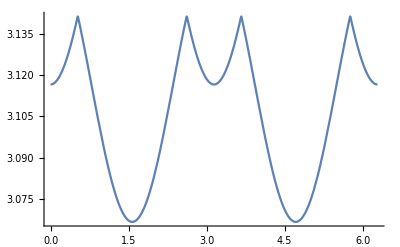

```mathematica
Plot[angles[[2]]/.{ww->1,H1->0.1},{phi,0,2Pi}]
```

```mathematica
coords3d=BlochCoordinatesFromState[ψf];
```

```mathematica
ParametricPlot[(Re[coords3d]/.{ww->1,H1->0.1})//Simplify,{phi,0,2Pi}]
```

-Graphics-

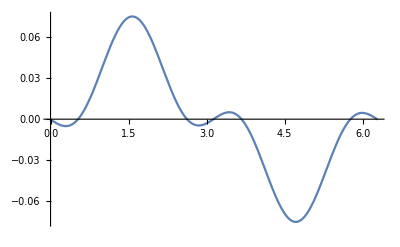

```mathematica
Plot[(Re[coords3d[[2]]]/.{ww->1,H1->0.1})//Simplify,{phi,0,2Pi}]
```